再谈模式

在 Wolfram 语言中，有一个完整的模式子语言。我们已经看到了其中的一些重要元素。

_ ("blank")可表示任意对象。x_ ("x blank")可表示任意对象，但名称为 x。_h 可表示任何标头为 h 的对象。而 x_h 表示标头为 h 的任何对象，名称为 x。

定义一个函数，其参数是一个名为 n 的整数：

```mathematica
digitback[n_Integer]:=Framed[Reverse[IntegerDigits[n]]]
```

只要参数是一个整数，该函数就会进行计算：

```mathematica
{digitback[1234],digitback[6712],digitback[x],digitback[{4,3,2}],digitback[2^32]}
```

{{4,3,2,1},{2,1,7,6},digitback[x],digitback[{4,3,2}],{6,9,2,7,6,9,4,9,2,4}}

有时你可能想在一个模式上设置一个条件。你可以用 /;。n_Integer/;n>0 表示任何大于 0 的整数。

给出一个只适用于 n>0 时的定义：

```mathematica
pdigitback[n_Integer/;n>0]:=Framed[Reverse[IntegerDigits[n]]]
```

这个定义并不适用于负数：

```mathematica
{pdigitback[1234],pdigitback[-1234],pdigitback[x],pdigitback[2^40]}
```

{{4,3,2,1},pdigitback[-1234],pdigitback[x],{6,7,7,7,2,6,1,1,5,9,9,0,1}}

/; 可以放在任何位置，甚至在整个定义的最后。

定义 check 函数的不同情况：

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[x_,y_]:=Green/;x≤y
```

check 函数的一些例子：

```mathematica
{check[1,2],check[2,1],check[3,4],check[50,60],check[60,50]}
```

{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

__ (“双 blank”)可表示任意一个或多个参数序列。___ (“三 blank”)可表示任意零个或多个。

定义一个函数，在一个列表中寻找黑色和白色(按照这个顺序)。

该模式匹配黑色，然后是白色，以及它们之前、之间和之后的任何元素：

```mathematica
blackwhite[{___,Black,m___,White,___}]:={1,m,2,m,3,m,4}
```

取出黑色和白色之间的(最小的)序列：

```mathematica
blackwhite[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],4}

默认情况下，__ 和 ___ 将选择最短的匹配。你可以使用 Longest 来使它们选择最长的。

指定黑色与白色之间的序列应尽可能长：

```mathematica
blackwhitex[{___,Black,Longest[m___],White,___}]:={1,m,2,m,3,m,4}
```

现在 m 将抓取一直到最后一个白色之间的元素：

```mathematica
blackwhitex[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],4}

x|y|z 可以匹配 x、y 或者 z。x.. 将匹配任意重复次数的 x。

bwcut 将有效地移除只包含黑色与白色的最长的一段：

```mathematica
bwcut[{a___,Longest[(Black|White)..],b___}]:={{a},Red,{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},RGBColor[1, 0, 0],{RGBColor[1, 1, 0]}}

模式 x_ 实际上是 x:_ 的缩写，意思是“匹配任何东西(即 _)并将结果命名为 x”。你也可以对更复杂的模式使用 x: 这样的符号。

建立一个名为 m 的模式，匹配一个由两对元素组成的列表：

```mathematica
grid22[m:{{_,_},{_,_}}]:=Grid[m,Frame->All]
```

```mathematica
{grid22[{{a,b},{c,d}}],grid22[{{12,34},{56,78}}],grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}
```

{a | b
c | d,12 | 34
56 | 78,grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}

为黑色与白色的序列起个名字，这样它就可以在结果中使用。

```mathematica
bwcut[{a___,r:Longest[(Black|White)..],b___}]:={{a},Framed[Length[{r}]],{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},5,{RGBColor[1, 1, 0]}}

举最后一个例子，让我们用模式来实现经典的计算机科学算法，即通过反复交换被发现不符合顺序的连续元素对来对一个列表进行排序。将算法中的每一步写成模式的替换是很容易的。

用符合顺序的元素来替换第一个发现的不符合顺序的元素：

```mathematica
{5,4,1,3,2}/.{x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{4,5,1,3,2}

同样的操作做 10 次，最终将列表完全排序：

```mathematica
NestList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2},10]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

在开始的时候，我们不会知道要花多长时间才能完成对某个特定列表的排序。所以最好的办法是使用 FixedPointList，它和 NestList 一样，只是你不必告诉它具体的步数，它会一直执行，直到结果达到一个固定的点，不再有任何变化。

执行操作，直到达到一个固定点：

```mathematica
FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

转置以找到在连续的步骤中出现的第一、第二 ... 等元素的列表：

```mathematica
Transpose[%]
```

{{4,4,1,1,1,1,1,1,1},{5,1,4,4,3,3,3,2,2},{1,5,5,3,4,4,2,3,3},{3,3,3,5,5,2,4,4,4},{2,2,2,2,2,5,5,5,5}}

ListLinePlot 将用不同的颜色来绘制每个列表，显示排序过程的进行情况：

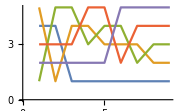

```mathematica
ListLinePlot[%]
```

下面是对一个长度为 20 的随机列表进行排序的结果：

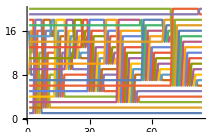

```mathematica
ListLinePlot[Transpose[FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[20]]]]]
```

词汇

patt/;cond |   | 如果满足条件才会进行匹配的模式
_ _ _ |   | 包含 0 个或者 多个元素的任意序列的模式(“三 blank”)
patt.. |   | 重复一个或多个 patt 的模式
Longest[patt] |   | 取出所匹配的最长的序列的模式
FixedPointList[f,x] |   | 持续嵌套 f，直到结果不再发生变化

"共有 12 道习题" | "开始练习 »"

计算 100 以内的数字的平方的各位数字，找出其中包含连续重复数字的数字列表。»

| 期望输出： |  
  | {{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}} |

在前 100 个罗马数字中，找出依次包含 L、I 和 X (三个字母不需要连续)的数字。»

| 期望输出： |  
  | {"XLIX","LIX","LXIX","LXXIX","LXXXIX"} |

定义一个函数 f，测试一个整数列表是否与它的反向相同。»

在维基百科上关于押韵(alliteration)的词条中，获取连续两个首字母相同的单词的列表。»

| 期望输出示例： |  
  | {{"same","sounds"},{"or","of"},{"stressed","syllables"},{"alphabet","and"},{"to","the"},{"to","the"},{"lazy","languid"},{"Peter","Piper"},{"Piper","Picked"},{"Pickled","Peppers"},{"wind","will"},{"agreement","akin"},{"to","the"},{"stressed","syllable"},{"as","alliterating"},{"of","outside"},{"same","sound"},{"of","outside"},{"to","the"},{"brown","blazers"},{"fundamentally","for"},{"colour","co-ordination"},{"in","its"},{"silken","sad"},{"furrow","followed"},{"followed","free"},{"stood","still"},{"Alphabetical","Africa"},{"chapter","consists"},{"at","all"},{"written","with"},{"Brent","Bernard"},{"who","watch"},{"watch","with"},{"with","wild"},{"wild","wonder"},{"wide","window"},{"beautiful","birds"},{"birds","begin"},{"bountiful","birdseed"},{"Grey","Geese"},{"grey","geese"},{"Betty","Botter"},{"Betty","Botter"},{"butter","but"},{"she","said"},{"butter's","bitter"},{"it","in"},{"make","my"},{"batter","bitter"},{"bitter","but"},{"better","butter"},{"make","my"},{"bitter","batter"},{"batter","better"},{"Peter","Piper"},{"Piper","Peter"},{"Peter","Piper"},{"pickled","peppers"},{"Peter","Piper"},{"pickled","peppers"},{"pickled","peppers"},{"Peter","Piper"},{"Irish","It"},{"important","ingredient"},{"Æthelwulf","Æthelbald"},{"Æthelbald","Æthelberht"},{"direct","descendants"},{"Tancred","Torhtred"},{"poetry","poets"},{"can","call"},{"splendid","silent"},{"silent","sun"},{"Walt","Whitman"},{"Splendid","Silent"},{"Silent","Sun"},{"wondered","what"},{"his","horse"},{"also","add"},{"to","the"},{"harsh","hard"},{"they","than"},{"slippered","sleep"},{"lean","lithe"},{"fleet","flown"},{"E.","E."},{"an","artistic"},{"that","the"},{"out","of"},{"as","an"},{"an","artistic"},{"constraint","can"},{"it","is"},{"emotional","effect"},{"as","a"},{"and","attention"},{"as","a"},{"persuasive","public"},{"any","attitude"},{"as","a"},{"adds","a"},{"an","audience’s"},{"audience’s","attention"},{"noticeable","nature"},{"evokes","emotion"},{"an","audience"},{"them","to"},{"to","the"},{"can","create"},{"is","in"},{"twenty-one","times"},{"times","throughout"},{"as","an"},{"which","we"},{"our","only"},{"of","our"},{"our","own"},{"but","by"},{"today","that"},{"that","the"},{"truths","that"},{"is","inextricably"},{"to","the"},{"itself","is"},{"testimony","to"},{"to","the"},{"have","had"},{"because","brave"},{"freedom's","front"},{"Ronald","Reagan"},{"Vietnam","Veterans"},{"new","nation"},{"to","the"},{"modern","music"},{"cartoon","characters"},{"If","I"},{"Anadiplosis","Assonance"},{"Tautogram","Tongue"},{"alliterations","and"}} |

使用 Grid 来显示本节中 {4,5,1,3,2} 的排序过程，将排序过程的每一步依次往下列出。»

| 期望输出： |  
  | 4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5 |

使用 ArrayPlot 来显示本节中长度为 50 的列表的排序过程，将排序过程按列显示。»

| 期望输出示例： |  
  | -Graphics- |

从 1.0 开始，然后反复应用 “牛顿法” 函数 (#+2/# )/2&，直到结果不再变化。»

| 期望输出： |  
  | {1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421} |

实现欧几里德的 GCD 算法，其中 {a,b} 反复被 {b,Mod[a,b]} 替换，直到 b 为 0，并将该算法应用于 12345，54321。»

| 期望输出： |  
  | {{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}} |

使用规则 s[x_][y_][z_]→x[z][y[z]],k[x_][y_]→x 来定义组合器(combinators)，然后从 s[s][k][s[s[s]][s]][s] 开始，应用这些规则直到没有变化，将所有结果生成一个列表。»

| 期望输出： |  
  | {s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]} |

从 100! 的各位数字的列表中删除位于末尾的所有 0。»

| 期望输出： |  
  | {9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4} |

从 {1,0} 开始，然后在 200 步内重复删除前 2 个元素，并且如果第一个元素是 1，则附加 {0,1}，如果是 0，则附加 {1,0,0}，为所得到的序列的长度创建一个列表(标签系统)。»

| 期望输出： |  
  | {2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125} |

从 {0,0} 开始，然后在 200 步内重复删除前 2 个元素，如果第一个元素是 0，则附加 {2,1}，如果第一个元素是 1，则附加 {0}，如果是 2，则附加 {0,2,1,2}，为所得到的序列的长度创建一个列表(标签系统)。»

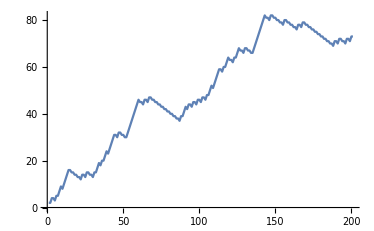
| 期望输出： |  
  | -Graphics- |

问&答

Wolfram 语言中还有哪些模式结构？

Except[patt] 将匹配除 patt 以外的任何东西。 PatternSequence[patt] 将匹配一个函数中的参数序列，OrderlessPatternSequence[patt] 将以任意顺序来匹配它们。f[x_:v] 将把 v 定义为默认值，所以 f[ ] 能被匹配，x 就是 v。

如何才能看到一个模式可能与一个特定表达式相匹配的所有方式？

使用 ReplaceList。Replace 将给出第一个匹配项；而 ReplaceList 将给出一个所有匹配项的列表。

如果没有固定点，FixedPointList 会发生什么？

它最终会停下来。有一个选项可以指定它要运行多久。FixedPointList[f,x,n] 将在最多运行 n 步之后停止。

技术笔记

在重复模式 patt.. 中，不要忘记在例如 0 .. 中留一个空格，以避免与小数数字混淆。

函数可以有影响模式匹配工作方式的属性。例如，Plus 包含 Flat 和 Orderless 属性。Flat 表示 b+c 可以从 a+b+c+d 中抽出。Orderless 表示元素可以被重新排序，所以 a+c 可以被抽出。(Flat 就像数学上的结合律；Orderless 就像交换律)。

所示的排序算法通常被称为冒泡排序。对于一个长度为 n 的列表，它通常需要大约 n^2 步。Wolfram 语言的内置函数 Sort 要快得多，只需要 n 步多一点。

探索更多

Wolfram 语言中的模式指南 »